```mathematica
(*Definición de matrices w*)
w={DiagonalMatrix[{1,-1,1}],DiagonalMatrix[{1,1,-1}], DiagonalMatrix[{-1,1,1}],DiagonalMatrix[{-1,-1,-1}]};
(*Definición de las funciones de distancia*)
TrDist[r_,s_]:=Sqrt[(r-s).(r-s)]/2;
Fid[r_,s_]:=(1+r.s)/2;
Aff[r_,s_]:=(r.s+(1+Sqrt[1-r.r]) (1+Sqrt[1-s.s]))/((Sqrt[1+Sqrt[r.r]]+Sqrt[1-Sqrt[r.r]]) (Sqrt[1+Sqrt[s.s]]+Sqrt[1-Sqrt[s.s]]));
WootersDist[r_,s_] := ArcCos[Sqrt[Fid[r, s]]];
Distances = {
{TrDist, "Trace Distance",N[8(11−2√10)/81]}, 
{Fid, "Fidelity",N[2/3]}, 
{Aff, "Affinity",N[√5/3] }, 
{WootersDist, "Wooters Distance",0.589}
};
```

```mathematica
(*Definición de los canales ruidosos*)
adM[x_]:=DiagonalMatrix[{Sqrt[1-x],Sqrt[1-x],1-x}];
adC[x_]:={0,0,x};
madM[x_]:=DiagonalMatrix[{Sqrt[1-x],Sqrt[1-x],1-x}];
madC[x_]:={0,0,-x};
chA = {adM, adC, "Amplitude Damping"};
chB = {madM, madC, "Mirrored Amplitude Damping"};
```

```mathematica
getLMax[pA_, pB_] := If[(1+√(1+2 pB-3 pB^2)<2 pA+pB), 3, 1];
```

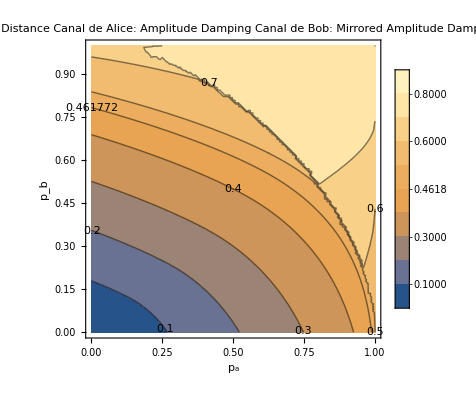

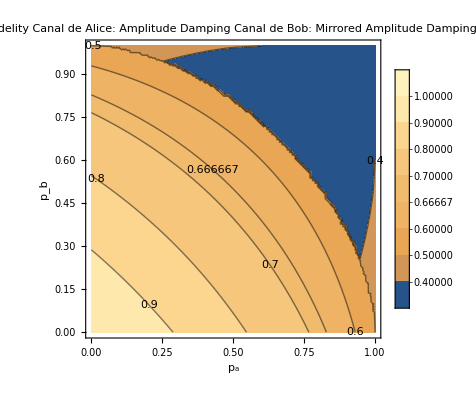

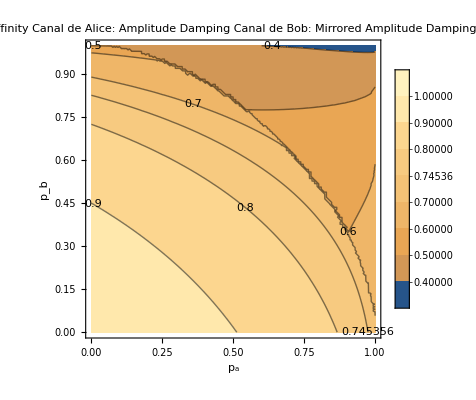

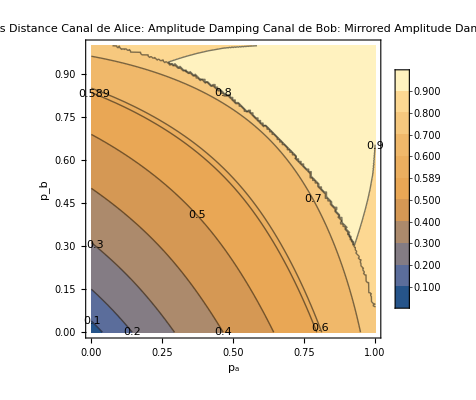

```mathematica
r=chA[[1]][pA].w[[1]].chB[[1]][pB]+Outer[Times,chA[[2]][pA],chB[[2]][pB]];
(*Vectores de Bloch de los estados reducidos de Alice y Bob*)
rA=chA[[2]][pA];
     rB=chB[[2]][pB];


RotOptFid[i_, pA_, pB_]:=w[[i]].w[[getLMax[pA,pB]]];

(*Definición de t,p[i] y tBob[i]*)
t={Cos[ϕ]*Sin[θ],Sin[ϕ]*Sin[θ],Cos[θ]};
     p[i_]:=(1+t.(w[[i]].rA))/4;
     tBob[i_, pA_, pB_]:=1/(4*p[i])*RotOptFid[i, pA,pB].(rB+Transpose[w[[i]].r].t);


Do[
(*Definición de AvgDist*)
AvgDist[pA_,pB_]:=1/(4 Pi) NIntegrate[Evaluate[Sum[p[i]*d[[1]][t,tBob[i, pA,pB]],{i,1,4}]*Sin[θ]],{ϕ,0,2 Pi},{θ,0,Pi}];

(*ContourPlot*)
Print[ContourPlot[AvgDist[pA,pB],{pA,0,1},{pB,0,1},
FrameLabel->{Style[Subscript[p,a],Black,Italic,24],Style[Subscript[p,b],Black,Italic,24]},
Contours->((contours = Sort[Append[FindDivisions[{#1,#2},#3], d[[3]]]])&),
(*Contours->((contours = Join[FindDivisions[{#1, d[[3]]},Quotient[#3,2]],{d[[3]]},  FindDivisions[{d[[3]],#2},Quotient[#3,2]-1]])&),*)
ContourLabels->All,
PlotLegends->Automatic, 
PlotLabel-> d[[2]] <> "\nCanal de Alice: " <> chA[[3]] <> "\nCanal de Bob: " <> chB[[3]] 
]]
,{d, Distances}]
```